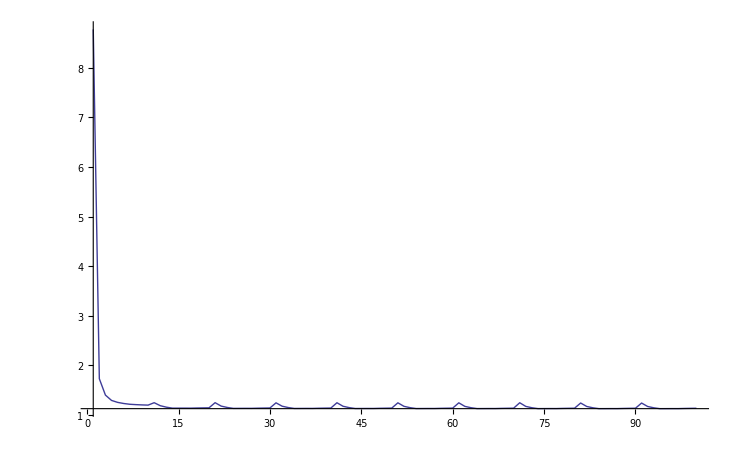

```mathematica
data = Import["C:\\Users\\PhycauseStudio\\Documents\\GitHub\\Fianl_Project\\results\\hidden_size = 10 vocab_size = 100\\perplexity_log_Epoch10.txt"];
perplecity = StringSplit[data];
perplecities  = ToExpression[perplecity];
ListPlot[perplecities  ,PlotRange->All,Joined->True,PlotStyle->{Thick,PointSize[Large]}]
```